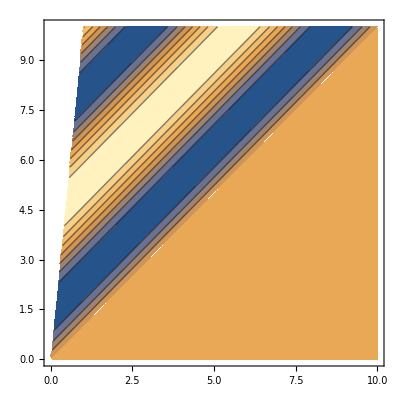

-Graphics3D-

ConditionalExpression[Piecewise[{{0, t≤x}, {0., True}}], 0.1 t≤x<t||x>t≥0]

ConditionalExpression[0, x>0]

ConditionalExpression[-2 Sin[1. t], t>0]

```mathematica
b=0.1;
g[s_]=0;
f[s_]=-2Sin[s];
u[x_,t_]=Piecewise[{{g[x-t], x>t>=0}, {f[(t-x)/(1-b)], b t<=x<t}, {Undefined, True}}];

ContourPlot[u[x,t],{x,0,10},{t,0,10},
PlotPoints->50]

Plot3D[u[x,t],{x,0,10},{t,0,10},
PlotPoints->30]

Manipulate[Plot[u[x,t],{x,0,10},
PlotRange->{{0,10},{-5,10}},
PlotPoints->200],
{t,0,10}]

D[u[x,t], t]+D[u[x,t], x]//FullSimplify
u[x,0]//FullSimplify
u[b t,t]//FullSimplify
```